# Neutron star surface locator

Author: George Pappas
Department of Physics, Aristotle University of Thessaloniki, Thessaloniki 54124, Greece

Reference: “The surface of rapidly-rotating neutron stars:  implications to neutron star parameter estimation”, Hector O. Silva, George Pappas, Nicolás Yunes and Kent Yagi, arxiv:xxxx-xxxxx (2020)

This notebook demonstrates the determination of the surface from an output file from the code RNS, developed by Stergioulas and Friedman, that produces rapidly rotating neutron stars.

The algorithm for finding the surface is based on locating the curve along which the enthalpy per unit mass becomes zero,  h=0.

```mathematica
pathread="/Users/pmzgp/Dropbox/Work/Mississippi\ work/expansion\ metric\ project/NS\ surface\ and\ ray\ tracing\ -\ NICER\ project/benchmark\ models/"
```

/Users/pmzgp/Dropbox/Work/Mississippi work/expansion metric project/NS surface and ray tracing - NICER project/benchmark models/

```mathematica
SetDirectory[pathread];
```

```mathematica
FileNames[]
```

{.DS_Store,eosSLy4_S_e_9.4769e14_r_0.69231.txt,eosSLy4_S_e_9.4769e14_r_0.73626.txt,eosSLy4_S_e_9.4769e14_r_0.78022.txt,eosSLy4_S_e_9.4769e14_r_0.82417.txt,eosSLy4_S_e_9.4769e14_r_0.86813.txt,eosSLy4_S_e_9.4769e14_r_0.91208_demo.txt,eosSLy4_S_e_9.4769e14_r_0.91208.txt,eosSLy4_S_e_9.4769e14_r_0.95604_demo.txt,eosSLy4_S_e_9.4769e14_r_0.95604.txt}

## Introduction

The output file generated with the RNS code, depending on the output option selected (see the RNS manual for this)  has different sections with different information regarding various stellar properties or the spacetime both inside and outside the star or the internal structure of the star.

In general one can select to have a full output with the stellar parameters and the spacetime and the internal structure variables of the star. This output though is quite large, therefore we have used a limited output that covers a relatively small region on both sides of the surface of the star, sufficient for the surface determination.

The following part of the code reads from the file the information stored in the various parts. 
The first part lists the various global properties of the star, such as Mass, Radius, Rotation rate, Angular Momentum, higher order multipole moments, and so on. 
In addition some other specific parameters are given, such as the scale used to compactify the radial coordinate r_e or the polar redshift Z_p, that we will use.
The second part lists the locations of the grid points in the compactified (x,μ) grid, where x=r/(r+r_e) and μ=cosθ, as well as the values of the metric functions of the metric 

ds^2 =- e^(γ+ρ)dt^2 + e^(2α) (dr^2+r^2 dθ^2) + r^2 e^(γ-ρ)sin^2 θ (dφ-ω dt)^2,

and the pressure and angular frequency of the star. The pressure is non-zero inside the star and goes to zero on the exterior, while for uniformly rotating stars the angular frequency Ω is everywhere constant.
As a final note, we point out that all angular frequencies given in RNS are given as Ω×10^-4 s, therefore a numerical value of 1 corresponds to 10^4 Hz.
Finally, the speed of light is assumed to be, c=299790 km/s.

```mathematica
MDIV=151;(*this is the number of the angular grid points*)
SetDirectory[pathread];
dataFileName="eosSLy4_S_e_9.4769e14_r_0.91208_demo.txt";
(*dataFileName="eosSLy4_S_e_9.4769e14_r_0.95604_demo.txt";*)
fileToRead1=dataFileName;
tableMoments=Import[fileToRead1,"Table"];
Dimensions[tableMoments]
tableData=Import[fileToRead1,"Table"];
Dimensions[tableData]
tabM1=Flatten[tableMoments[[5]]];
tabM2=Flatten[tableMoments[[7]]];
mdelsTab[1]=Table[{tabM1[[i]],tabM2[[i]]},{i,1,Dimensions[tabM1][[1]]}];
Print["====================="];
Print["Model's global parameters and various properties"];
Print["====================="];
Print[Table[{tabM1[[i]],tabM2[[i]]},{i,1,Dimensions[tabM1][[1]]}]//MatrixForm];
re=tabM2[[16]];(*this is the scale of the radial compactification*)
Print[re];
Zp=tabM2[[12]];(*this is the polar redshift*)
nuP=-Log[Zp+1];
Print[nuP];
ParNS[1]={tabM2[[31]],tabM2[[16]],tabM2[[4]],tabM2[[5]] 10^4,tabM2[[5]](2 π)^-1 10^4,(tabM2[[5]] 1000/29979)^2 tabM2[[4]]^3/tabM2[[31]],tabM2[[4]]/tabM2[[31]],tabM2[[33]],tabM2[[41]]};Print[{{"M(km)","r_e(km)","Re(km)","Ω(Hz)","f(Hz)","σ=Ω^2Re^3/M","κ^-1=Re/M","J(km^2)","Q(km^3)"},ParNS[1]}//MatrixForm];
Print["====================="];
Print["Model's spacetime and fluid variables on the grid"];
Print["====================="];
Print[tableData[[10]]];
numtable=Table[tableData[[11+i]],{i,1,Dimensions[tableData][[1]]-11}];
Print[numtable[[1]]];
Print[numtable[[2]]];
Print[numtable[[3]]];
Print["..."];
Print[numtable[[-MDIV]]];
Print[numtable[[-MDIV+1]]];
Print[numtable[[-MDIV+2]]];
Print["..."];
Print[numtable[[-1]]];
Dimensions[numtable]
Dimensions[numtable][[1]]/MDIV(*this is the number of the radial grid points in the output*)
```

{9071}

{9071}

=====================

Model's global parameters and various properties

=====================

(rho_c | 9.4769×10^14
M | 1.4092
M_0 | 1.54996
R | 12.2709
Omega | 0.366551
Omega_p | 1.00058
T/W | 0.0242199
C*J/GM_s^2 | 0.610597
I | 1.46397
h_plus | 0.
h_minus | 2.90004
Z_p | 0.249394
Z_b | 0.485732
Z_f | 0.0233392
omega_c/Omega | 0.449795
r_e | 10.0585
r_ratio | 0.91208
Omega_pa | 1.00058
Omega+ | 1.00058
u_phi | 4.5834
r_plus | 0.
r_minus | 12.9928
exp_gamma_eq | 0.989628
exp_gamma_plus | 1.
exp_gamma_minus | 0.993811
conv_rad | 1.21996
conv_plus | 1.
conv_minus | 1.16764
chi | 0.307475
q | -0.454168
Mgeom | 2.07908
M2_geom | -4.07911
Jgeom | 1.32908
S3_geom | -5.19845
M2_asy | -54.9703
M2 | -54.937
S3_asy | -0.210048
S3 | -0.20989
B0_geom | -1.03799
B0/M^2 | -0.240133
M2^GH_geom | -4.19734
S3^GH_geom | -5.33449
M4_geom | 36.1156
M4_asy^GH_geom | 60.9586
B2/M^4 | 0.0591761
S5_geom | -5994.52
B2_asy/M^4 | 744087.
M4_asy_geom | 60.1745
S5_asy_geom | -2.95691×10^7
M4_geom_2points | 20.5058
M4_geom_3points | 19.5365
M4_geom_4points | 19.2621)

10.0585

-0.222659

(M(km) | r_e(km) | Re(km) | Ω(Hz) | f(Hz) | σ=Ω^2Re^3/M | κ^-1=Re/M | J(km^2) | Q(km^3)
2.07908 | 10.0585 | 12.2709 | 3665.51 | 583.384 | 0.132859 | 5.90208 | 1.32908 | -4.19734)

=====================

Model's spacetime and fluid variables on the grid

=====================

{r/(r+r_e),cos(theta),rho,gamma,alpha,omega,pressure,Omega}

{0.329967,0.,-0.684044,-0.0340158,0.324143,0.124922,5.03487×10^34,0.366551}

{0.329967,0.00666667,-0.684044,-0.0340157,0.324143,0.124922,5.03484×10^34,0.366551}

{0.329967,0.0133333,-0.684042,-0.0340155,0.324142,0.124921,5.03475×10^34,0.366551}

...

{0.526614,0.,-0.3669,-0.00839907,0.178643,0.0337992,0.,0.366551}

{0.526614,0.00666667,-0.3669,-0.00839905,0.178643,0.0337991,0.,0.366551}

{0.526614,0.0133333,-0.366899,-0.00839901,0.178642,0.0337988,0.,0.366551}

...

{0.526614,1.,-0.359008,-0.00812061,0.175444,0.0316517,0.,0.366551}

{9060,8}

60

In the above printout one can see the format of the data table with the grid points and the metric and fluid variables. 
(rho, gamma, alpha, omega) are the metric functions.
“pressure” is the pressure.
“Omega” is the stellar angular frequency.

## Finding the surface

The surface is indicated by the zero of the function  

h  =  ln u^t + ((ρ+γ)/2)_(pol.),

where u^t is the four-velocity of a fluid element of the star, while the last term on the right is essentially related to the redshift at the pole of the star. The RNS code gives apart from the usual quantities, some additional “physical parameters”, including the redshift at the pole of the star, Z_p. Therefore, the last term in the above equation can be calculated from Z_p and it is equal to -ln(1+Z_p).

Here we plot the contours of this function and find the curve along which it becomes h=0.

```mathematica
contourPlotTab2=Table[{re numtable[[i,1]]/(1-numtable[[i,1]]) Exp[(numtable[[i,4]]-numtable[[i,3]])/2],numtable[[i,2]],nuP+Log[Exp[-(numtable[[i,3]]+numtable[[i,4]])/2]/(√(1-(re numtable[[i,1]]/(1-numtable[[i,1]]))^2(1-numtable[[i,2]]^2)Exp[-2 numtable[[i,3]]](numtable[[i,8]]-numtable[[i,6]])^2(1000/29979)^2))]},{i,1,Dimensions[numtable][[1]]}];
surfaceTabNew=Table[Null,{i,1,MDIV}];
For[j=1,j<MDIV+1,enthalpy=Interpolation[Table[{contourPlotTab2[[i,1]],contourPlotTab2[[i,3]]},{i,j,Dimensions[contourPlotTab2][[1]],MDIV}]];Rsurf=x/.FindRoot[enthalpy[x],{x,contourPlotTab2[[1,1]]+1}];surfaceTabNew[[j]]={Rsurf,contourPlotTab2[[j,2]]};j=j+1;];
```

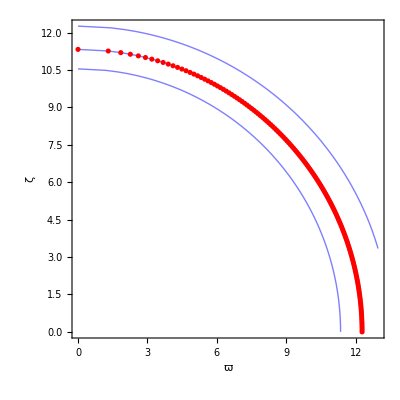

```mathematica
Show[ListContourPlot[Table[{contourPlotTab2[[i,1]] √(1- contourPlotTab2[[i,2]]^2),contourPlotTab2[[i,1]] contourPlotTab2[[i,2]],contourPlotTab2[[i,3]]},{i,1,Dimensions[contourPlotTab2][[1]]}],ContourShading->False,ContourStyle->Blue,Contours->{-0.02,0,0.02}],ListPlot[Table[{surfaceTabNew[[i,1]] √(1- surfaceTabNew[[i,2]]^2),surfaceTabNew[[i,1]]  surfaceTabNew[[i,2]]},{i,1,151}],PlotStyle->Red],PlotRange->All,Axes->False,Frame->True,FrameLabel->{"ϖ","ζ"}]
```

The following contour plot is similar to the one in the paper.

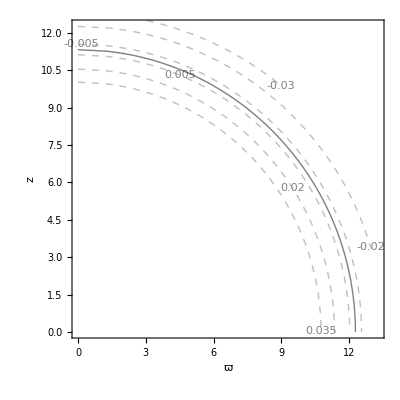

```mathematica
Show[ListContourPlot[Table[{contourPlotTab2[[i,1]] √(1- contourPlotTab2[[i,2]]^2),contourPlotTab2[[i,1]] contourPlotTab2[[i,2]],contourPlotTab2[[i,3]]},{i,1,Dimensions[contourPlotTab2][[1]]}],ContourShading->False,ContourStyle->{{Gray,Thick,Dashed}},Contours->{-0.03,-0.02,-0.005,0.005,0.02,0.035},ContourLabels->Function[{x,y,z},Text[Style[z,Gray],{x,y},Background->None]]],ListContourPlot[Table[{contourPlotTab2[[i,1]] √(1- contourPlotTab2[[i,2]]^2),contourPlotTab2[[i,1]] contourPlotTab2[[i,2]],contourPlotTab2[[i,3]]},{i,1,Dimensions[contourPlotTab2][[1]]}],ContourShading->False,Contours->{0},ContourStyle->{{Black,Thick}}],FrameLabel->{"ϖ","z"},BaseStyle->{FontSize->18,FontFamily->"Times"},PlotRange->{{0,tabM2[[4]]+1},{0,tabM2[[4]]}}]
```

## Calculating the relevant surface functions

For our analysis in the paper, there are two relevant functions that we need. The first is the function of the surface itself, R(μ) and the other is the function (d log R(μ))/dθ. 
In what follows, we first interpolate the function R(μ) and then from the interpolated function calculate (d log R(μ))/dθ.

```mathematica
testSurfTab=surfaceTabNew;
Dimensions[testSurfTab]
Rsurface=Interpolation[Table[{testSurfTab[[i,2]],testSurfTab[[i,1]]},{i,1,MDIV}]]
```

{151,2}

InterpolatingFunction[…]

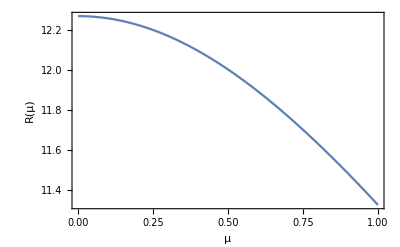

```mathematica
Plot[Rsurface[x],{x,0,1},Axes->False,Frame->True,FrameLabel->{"μ","R(μ)"}]
```

```mathematica
dlogR=D[Log[Rsurface[x]],x]
```

(InterpolatingFunction[…][x])/(InterpolatingFunction[…][x])

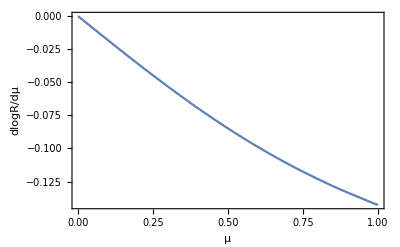

```mathematica
Plot[dlogR,{x,0,1},Axes->False,Frame->True,FrameLabel->{"μ","dlogR/dμ"}]
```

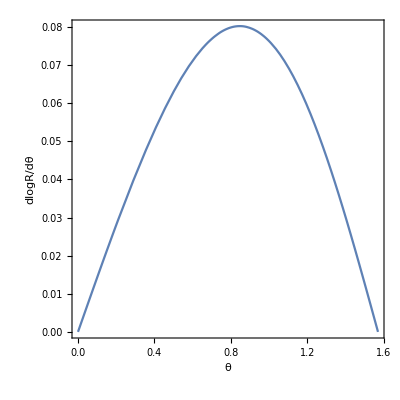

```mathematica
ParametricPlot[{ArcCos[x],-dlogR √(1-x^2)},{x,0,1},Axes->False,Frame->True,FrameLabel->{"θ","dlogR/dθ"},AspectRatio->1]
```

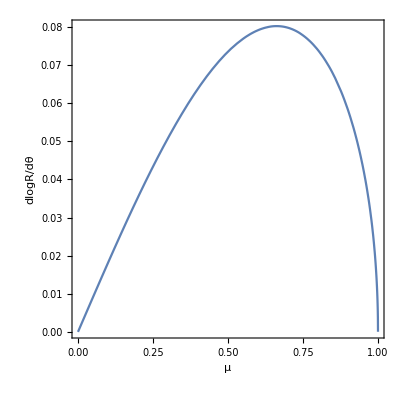

```mathematica
Plot[-dlogR √(1-x^2),{x,0,1},Axes->False,Frame->True,FrameLabel->{"μ","dlogR/dθ"},AspectRatio->1]
```

While here we calculate (d log R(μ))/dθ numerically, using the symmetric difference quotient, and compare this against the result from the interpolated functions and observe a very good agreement.

```mathematica
dLogRdμTab=Table[{testSurfTab[[i,2]],If[i==1,0,If[i==151,0,-√(1-testSurfTab[[i,2]]^2)(Log[testSurfTab[[i+1,1]]]-Log[testSurfTab[[i-1,1]]])/(testSurfTab[[i+1,2]]-testSurfTab[[i-1,2]])]]},{i,1,MDIV}];
```

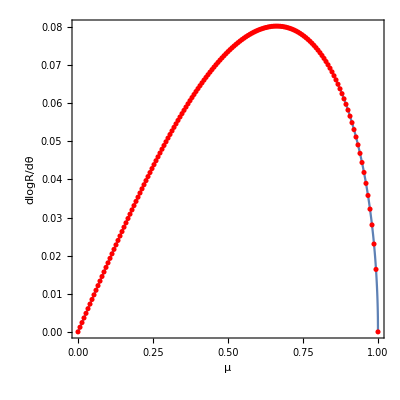

```mathematica
Show[Plot[-dlogR √(1-x^2),{x,0,1},Axes->False,Frame->True,FrameLabel->{"μ","dlogR/dθ"},AspectRatio->1],ListPlot[dLogRdμTab,PlotStyle->Red],Axes->False,Frame->True]
```

In the paper, we describe a more sophisticated approach in calculating  R(μ) and (d log R(μ))/dθ, that gives very accurate results.